```mathematica
Clear["Global`*"];
(*AG长度*)
d=1.40792;
(*弹簧原长度*)
l0=0.5;
(*振子质量*)
m=2433;
(*弹簧劲度系数*)
k=80000;
(*直线阻尼器阻尼系数*)
c=10000;
(*小g*)
g=9.8;
(*弹簧旋转刚度*)
krot=250000;
(*旋转阻尼器阻尼系数*)
crot=1000;
(*浮子质量*)
M=4866;
(*垂荡兴波阻尼系数*)
c0=683.4558;
(*纵摇附加转动惯量*)
I0=7001.914;
(*纵摇激励力矩振幅*)
L=1690;
(*入射波浪频率*)
w=1.7152;
(*垂荡激励力振幅*)
f=3640;
(*浮子转动惯量*)
(*Ia=300*4866/(7π+(Sqrt[41]π)/5)*(Integrate[1/0.8*2*Pi*(r+(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5))*r^2,{r,-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5),-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5)+0.8}]+Integrate[2*Pi*r^2,{r,-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5)+0.8,-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5)+3.8}]+Integrate[2*Pi*(3.8-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5))^2+a^2,{a,0,0.5}]);*)
Ia=8399.2;

(*垂荡附加质量*)
m0=1028.876;
(*纵摇兴波阻尼力矩系数*)
cr0=654.3383;
(*纵摇静水恢复力矩系数*)
Mrec=8890.7;
(*海水密度*)
rho=1025;

(*垂荡静水恢复力(浮力)*)
Fj[t_]:=(7.120975609756098-Pi*zg[t])*rho*g;
(*激励力*)
Fwave[t_]:=f*Cos[w*t];
(*振子转动惯量*)
(*Ib[t_]:=258.149+774.448l[t]+1548.9l[t]^2;*)
(*Ib[t_]:=MomentOfInertia[Cylinder[{{0,0,0},{0.5,0,0}},0.5],{l[t]+0.5,0,0},{0,0,1}]*)
Ib[t_]:=m/12*(4*0.5^2-12*0.5*(0.5+l[t])+3*1^2+12*(0.5+l[t])^2)
(*纵摇激励力矩*)
Mwave[t_]:=L*Cos[w*t];
(*theta2=theta1+gamma*)
th2[t_]:=th[t]+ga[t];
(*P点x座标*)
xp[t_]:=xg[t]+d*Sin[th[t]]-l[t]*Sin[th2[t]];
(*P点z座标*)
zp[t_]:=zg[t]-d*Cos[th[t]]+l[t]*Cos[th2[t]];
(*PTO系统的力*)
Fpto[t_]:=-k*(l[t]-l0)-c*l'[t];
(*PTO系统的力矩*)
Mpto[t_]:=-krot*ga[t]-crot*ga'[t];

start=0;
stop=start+100;
```

```mathematica
group={m*xp''[t]==-Fpto[t]*Sin[th2[t]]+Fab[t]*Cos[th2[t]],m*zp''[t]==Fpto[t]*Cos[th2[t]]-m*g+Fab[t]*Sin[th2[t]],Ib[t]*th2''[t]==Mpto[t]+Fab[t]*l[t],M*zg''[t]==Fwave[t]+Fj[t]-M*g-Fpto[t]*Cos[th2[t]]-Fab[t]*Sin[th2[t]]-m0*zg''[t]-c0*zg'[t],Ia*th''[t]==Mwave[t]-Mpto[t]+Fab[t]*d*Cos[th[t]]*Cos[th2[t]]-Fab[t]*d*Sin[th[t]]*Sin[th2[t]]-I0*th''[t]-cr0*th'[t]-Mrec*th[t],M*xg''[t]==Fpto[t]*Sin[th2[t]]-Fab[t]*Cos[th2[t]],th'[0]==th[0]==ga[0]==ga'[0]==l'[0]==zg'[0]==xg[0]==xg'[0]==Fab[0]==Fab'[0]==0,l[0]==l0-m/k,zg[0]==0};
```

```mathematica
s=NDSolve[group,{th,ga,zg,l, xg},{t,start,stop}];
```

NDSolve::pdord: 某些函数的微分阶数为零，因此方程将作为微分代数方程组求解.

NDSolve::ivres: 对于微分代数系统，NDSolve 已经计算了给出零残差的初始值，但是某些分量与指定的不同. 如果它们需要被满足，建议您对所有应变量和它们的导数给出初始条件.

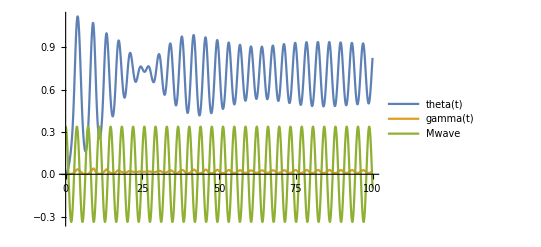

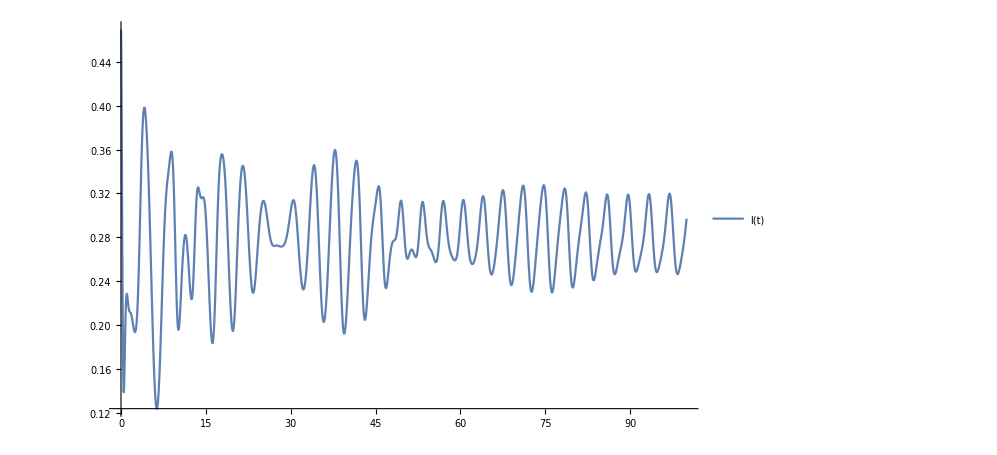

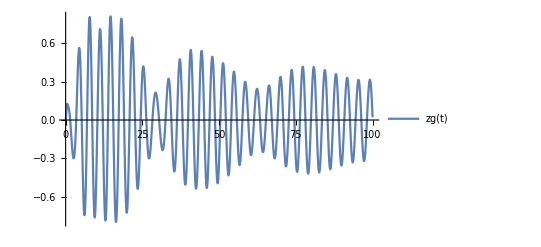

```mathematica
Plot[{th[t]/.s,ga[t]/.s,Mwave[t]/5000},{t,start,stop},PlotLegends->{"theta(t)","gamma(t)","Mwave"}]
Plot[l[t]/.s,{t,start,stop},PlotLegends->{"l(t)"}]
Plot[zg[t]/.s,{t,start,stop},PlotLegends->{"zg(t)"}]
```

```mathematica
Plot[Fj[t]/.s,{t,0,stop},PlotLegends->{"F浮"}]
```

NDSolve::dsvar: 0.00204286 不能用作变量.

ReplaceAll::reps: {NDSolve[{2433 (-1.40792 Sin[«1»] Power[«2»]-2 Cos[«1»] («1»)^(«1»)[«1»] Plus[«2»]+l[«1»] Sin[«1»] Power[«2»]-Sin[«1»] («1»)^(«1»)[«1»]+1.40792 Cos[«1»] («1»)^(«1»)[«1»]-Cos[«1»] l[«1»] Plus[«2»])==Cos[Plus[«2»]] Fab[0.00204286]+Sin[Plus[«2»]] (Times[«2»]+Times[«2»]),«7»,zg[0]==0},{th,ga,zg,l,xg,Fab},{0.00204286,0,100}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

NDSolve::dsvar: 0.00204286 不能用作变量.

ReplaceAll::reps: {NDSolve[{2433. (-1.40792 Sin[«1»] Power[«2»]-2. Cos[«1»] («1»)^(«1»)[«1»] Plus[«2»]+l[«1»] Sin[«1»] Power[«2»]-1. Sin[«1»] («1»)^(«1»)[«1»]+1.40792 Cos[«1»] («1»)^(«1»)[«1»]-1. Cos[«1»] l[«1»] Plus[«2»])==Cos[Plus[«2»]] Fab[0.00204286]+Sin[Plus[«2»]] (Times[«2»]+Times[«2»]),«7»,zg[0.]==0.},{th,ga,zg,l,xg,Fab},{0.00204286,0.,100.}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

NDSolve::dsvar: 2.04286 不能用作变量.

General::stop: 在本次计算中，NDSolve::dsvar 的进一步输出将被抑制.

ReplaceAll::reps: {NDSolve[{2433 (-1.40792 Sin[«1»] Power[«2»]-2 Cos[«1»] («1»)^(«1»)[«1»] Plus[«2»]+l[«1»] Sin[«1»] Power[«2»]-Sin[«1»] («1»)^(«1»)[«1»]+1.40792 Cos[«1»] («1»)^(«1»)[«1»]-Cos[«1»] l[«1»] Plus[«2»])==Cos[Plus[«2»]] Fab[2.04286]+Sin[Plus[«2»]] (Times[«2»]+Times[«2»]),«7»,zg[0]==0},{th,ga,zg,l,xg,Fab},{2.04286,0,100}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

General::stop: 在本次计算中，ReplaceAll::reps 的进一步输出将被抑制.

-Graphics-

```mathematica
(*s1=NDSolve[{Derivative[1][x][t]^2+x[t]^2==1,x[0]==1/2},x,{t,0,10Pi},Method->{"EquationSimplification"->"Residual"}]*)
(*NDSolve[{y''[t]==-y[t],y[0]==1,y'[0]==0},y,{t,0,1},Method->{"TimeIntegration"->"ExplicitEuler"}]*)
(*NDSolve[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,30},Method->{"TimeIntegration"->"ExplicitRungeKutta"}]*)
```